### Iteration 1

```mathematica
A = ({{α, 0, 0}, {0, β, 0}, {0, 0, γ}});
H = ({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}});
Subscript[q, 1] = {1,0,0};
Subscript[q, 2] = A.Subscript[q, 1] +{Subscript[ξ, 1,1],Subscript[ξ, 1,2],Subscript[ξ, 1,3]};
H[[1,1]] = Subscript[q, 1].Subscript[q, 2];
Subscript[q, 2] = Subscript[q, 2] - H[[1,1]]* Subscript[q, 1];
H[[2,1]] = √(Subscript[q, 2].Subscript[q, 2]);
Subscript[q, 2] = Subscript[q, 2]/H[[2,1]];
(*Subscript[σ, 1] = Eigenvalues[H[[1;;3]]]*)
Subscript[σ, 1] = H[[1,1]];
H //MatrixForm
```

(α+ξ_(1,1) | 0 | 0
√(ξ_(1,2)^2+ξ_(1,3)^2) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### Iteration 2

```mathematica
Subscript[q, 3] = A.Subscript[q, 2] +{Subscript[ξ, 2,1],Subscript[ξ, 2,2],Subscript[ξ, 2,3]};
H[[1,2]] = Subscript[q, 1].Subscript[q, 3];
H[[2,2]] = Subscript[q, 2].Subscript[q, 3];
Subscript[q, 3] = Subscript[q, 3] - H[[1,2]] Subscript[q, 1];
Subscript[q, 3] = Subscript[q, 3] - H[[2,2]] Subscript[q, 2];
Subscript[q, 3] = Simplify[Subscript[q, 3]];
H[[3,2]] = Simplify[√(Subscript[q, 3].Subscript[q, 3])];
Subscript[q, 3] = Subscript[q, 3]/H[[3,2]];
Subscript[q, 3] = FullSimplify[Subscript[q, 3]];
Subscript[σ, 2] = Eigenvalues[H[[1;;2,1;;2]]];
H//MatrixForm
```

(α+ξ_(1,1) | ξ_(2,1) | 0
√(ξ_(1,2)^2+ξ_(1,3)^2) | (ξ_(1,2) ((β ξ_(1,2))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+ξ_(2,2)))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+(ξ_(1,3) ((γ ξ_(1,3))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+ξ_(2,3)))/(√(ξ_(1,2)^2+ξ_(1,3)^2)) | 0
0 | √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)) | 0
0 | 0 | 0)

## Taylor Series Expansion–These are only valid for α≥β≥γ! And I made some mistakes in the expectedValue

```mathematica
a=Series[Subscript[σ, 2][[1]],{Subscript[ξ, 1,1],0,3},{Subscript[ξ, 1,2],0,3},{Subscript[ξ, 1,3],0,3},{Subscript[ξ, 2,1],0,3},{Subscript[ξ, 2,2],0,3},{Subscript[ξ, 2,3],0,3},{Subscript[ξ, 3,1],0,3},{Subscript[ξ, 3,2],0,3},{Subscript[ξ, 3,3],0,3}];
```

```mathematica
a = Normal[Simplify[a]]
```

1/2 (α-√((α-γ)^2)+γ)+((-α+√((α-γ)^2)+γ) ξ_(1,1))/(2 √((α-γ)^2))-((α+√((α-γ)^2)-γ) (-β+γ) ξ_(1,2)^2)/(2 √((α-γ)^2) ξ_(1,3)^2)+(((-((α+2 β-3 γ) √((α-γ)^2))/(2 (α-γ)^3)+((α+4 β-5 γ) ξ_(1,1))/(2 ((α-γ)^2)^(3/2))-((α+6 β-7 γ) √((α-γ)^2) ξ_(1,1)^2)/(2 (α-γ)^5)+((α+8 β-9 γ) √((α-γ)^2) ξ_(1,1)^3)/(2 (α-γ)^6)) ξ_(1,2)^2)/(ξ_(1,3))+(-1/(√((α-γ)^2))+(√((α-γ)^2) ξ_(1,1))/(α-γ)^3-(√((α-γ)^2) ξ_(1,1)^2)/(α-γ)^4+(√((α-γ)^2) ξ_(1,1)^3)/(α-γ)^5) ξ_(1,3)) ξ_(2,1)+((((α+3 β-4 γ) √((α-γ)^2))/(α-γ)^5-(3 (α+4 β-5 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^6+(6 (α+5 β-6 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7-(10 (α+6 β-7 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^2+(1/(((α-γ)^2)^(3/2))-(3 √((α-γ)^2) ξ_(1,1))/(α-γ)^5+(6 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6-(10 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,3)^2) ξ_(2,1)^2+(((-3 α-10 β+13 γ)/((α-γ)^5 √((α-γ)^2))+(15 (α+4 β-5 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(15 (3 α+14 β-17 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(35 (3 α+16 β-19 γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^2 ξ_(1,3)+(-2/(((α-γ)^2)^(5/2))+(10 √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(70 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,3)^3) ξ_(2,1)^3+(((-α-√((α-γ)^2)+γ) ξ_(1,2)^3)/(4 √((α-γ)^2) ξ_(1,3)^3)+((α+√((α-γ)^2)-γ) ξ_(1,2))/(2 √((α-γ)^2) ξ_(1,3))+((-(√((α-γ)^2))/(α-γ)^3+(2 ξ_(1,1))/(((α-γ)^2)^(3/2))-(3 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^5+(4 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^6) ξ_(1,2)+(((2 (-β+γ))/(((α-γ)^2)^(3/2))+(6 (β-γ) ξ_(1,1))/((α-γ)^3 √((α-γ)^2))+(12 √((α-γ)^2) (-β+γ) ξ_(1,1)^2)/(α-γ)^6+(20 (β-γ) ξ_(1,1)^3)/((α-γ)^5 √((α-γ)^2))) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+((((3 (α+8 β-9 γ) √((α-γ)^2))/(2 (α-γ)^6)-(6 (α+10 β-11 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(15 (α+12 β-13 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(30 (α+14 β-15 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^3)/(ξ_(1,3))+((3 √((α-γ)^2))/(α-γ)^5-(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6+(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+((-(10 (α+6 β-7 γ) √((α-γ)^2))/(α-γ)^8+(60 (α+7 β-8 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(210 (α+8 β-9 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))+(560 (α+9 β-10 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^3+(-(10 √((α-γ)^2))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+(((-(√((α-γ)^2))/(α-γ)^4+(3 √((α-γ)^2) ξ_(1,1))/(α-γ)^5-(6 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6+(10 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+((6 √((α-γ)^2))/(α-γ)^6-(30 √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(90 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2 ξ_(2,1)^2+(-(30 √((α-γ)^2))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(840 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10+(2520 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+(((-(√((α-γ)^2))/(α-γ)^5+(4 √((α-γ)^2) ξ_(1,1))/(α-γ)^6-(10 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7+(20 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+(((10 √((α-γ)^2))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+(-(70 √((α-γ)^2))/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1))/(α-γ)^10-(2520 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11+(8400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3+(1/4 (2+(2 (α-γ))/(√((α-γ)^2)))+((-α-√((α-γ)^2)+γ) ξ_(1,2)^2)/(4 √((α-γ)^2) ξ_(1,3)^2)+((((2 (-β+γ))/(((α-γ)^2)^(3/2))+(6 (β-γ) ξ_(1,1))/((α-γ)^3 √((α-γ)^2))+(12 √((α-γ)^2) (-β+γ) ξ_(1,1)^2)/(α-γ)^6+(20 (β-γ) ξ_(1,1)^3)/((α-γ)^5 √((α-γ)^2))) ξ_(1,2)^2)/(ξ_(1,3))+(-(√((α-γ)^2))/(α-γ)^3+(2 ξ_(1,1))/(((α-γ)^2)^(3/2))-(3 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^5+(4 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^6) ξ_(1,3)) ξ_(2,1)+(((3 (α+8 β-9 γ) √((α-γ)^2))/(2 (α-γ)^6)-(6 (α+10 β-11 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(15 (α+12 β-13 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(30 (α+14 β-15 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2+((3 √((α-γ)^2))/(α-γ)^5-(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6+(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,3)^2) ξ_(2,1)^2+((-(10 (α+6 β-7 γ) √((α-γ)^2))/(α-γ)^8+(60 (α+7 β-8 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(210 (α+8 β-9 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))+(560 (α+9 β-10 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^2 ξ_(1,3)+(-(10 √((α-γ)^2))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,3)^3) ξ_(2,1)^3+(((-2/(((α-γ)^2)^(3/2))+(6 √((α-γ)^2) ξ_(1,1))/(α-γ)^5-(12 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6+(20 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,2)+(((√((α-γ)^2) (α-6 β+5 γ))/(α-γ)^5-(3 √((α-γ)^2) (α-8 β+7 γ) ξ_(1,1))/(α-γ)^6+(6 √((α-γ)^2) (α-10 β+9 γ) ξ_(1,1)^2)/(α-γ)^7-(10 √((α-γ)^2) (α-12 β+11 γ) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+((((60 (β-γ))/((α-γ)^5 √((α-γ)^2))+(360 √((α-γ)^2) (-β+γ) ξ_(1,1))/(α-γ)^8+(1260 √((α-γ)^2) (β-γ) ξ_(1,1)^2)/(α-γ)^9+(3360 (-β+γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^3)/(ξ_(1,3))+((12 √((α-γ)^2))/(α-γ)^6-(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(180 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(420 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+((-(30 (α+14 β-15 γ) √((α-γ)^2))/(α-γ)^9+(210 (α+16 β-17 γ) ξ_(1,1))/((α-γ)^8 √((α-γ)^2))-(840 (α+18 β-19 γ) ξ_(1,1)^2)/((α-γ)^9 √((α-γ)^2))+(2520 (α+20 β-21 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3+(-(60 √((α-γ)^2))/(α-γ)^8+(420 √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10+(5040 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+(((-(3 √((α-γ)^2))/(α-γ)^5+(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6-(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+((30 √((α-γ)^2))/(α-γ)^7-(180 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(630 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^2 ξ_(2,1)^2+(-(210 √((α-γ)^2))/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10-(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+(((-(4 √((α-γ)^2))/(α-γ)^6+(20 √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(140 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+(((60 √((α-γ)^2))/(α-γ)^8-(420 √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10-(5040 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+(-(560 √((α-γ)^2))/(α-γ)^10+(5040 √((α-γ)^2) ξ_(1,1))/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12+(92400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3) ξ_(2,3)+(((((√((α-γ)^2) (α-6 β+5 γ))/(2 (α-γ)^5)-(3 √((α-γ)^2) (α-8 β+7 γ) ξ_(1,1))/(2 (α-γ)^6)+(3 √((α-γ)^2) (α-10 β+9 γ) ξ_(1,1)^2)/(α-γ)^7-(5 √((α-γ)^2) (α-12 β+11 γ) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^2)/(ξ_(1,3))+(-1/(((α-γ)^2)^(3/2))+(3 √((α-γ)^2) ξ_(1,1))/(α-γ)^5-(6 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6+(10 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,3)) ξ_(2,1)+(((30 (β-γ))/((α-γ)^5 √((α-γ)^2))+(180 √((α-γ)^2) (-β+γ) ξ_(1,1))/(α-γ)^8+(630 √((α-γ)^2) (β-γ) ξ_(1,1)^2)/(α-γ)^9+(1680 (-β+γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^2+((6 √((α-γ)^2))/(α-γ)^6-(30 √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(90 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,3)^2) ξ_(2,1)^2+((-(15 (α+14 β-15 γ) √((α-γ)^2))/(α-γ)^9+(105 (α+16 β-17 γ) ξ_(1,1))/((α-γ)^8 √((α-γ)^2))-(420 (α+18 β-19 γ) ξ_(1,1)^2)/((α-γ)^9 √((α-γ)^2))+(1260 (α+20 β-21 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^2 ξ_(1,3)+(-(30 √((α-γ)^2))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(840 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10+(2520 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,3)^3) ξ_(2,1)^3+(((-(3 √((α-γ)^2))/(α-γ)^5+(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6-(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)+(((3 √((α-γ)^2) (α-4 β+3 γ))/(α-γ)^6-(12 √((α-γ)^2) (α-5 β+4 γ) ξ_(1,1))/(α-γ)^7+(30 √((α-γ)^2) (α-6 β+5 γ) ξ_(1,1)^2)/(α-γ)^8-(60 √((α-γ)^2) (α-7 β+6 γ) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+(((-(15 √((α-γ)^2) (α-12 β+11 γ))/(α-γ)^8+(90 √((α-γ)^2) (α-14 β+13 γ) ξ_(1,1))/(α-γ)^9-(315 (α-16 β+15 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))+(840 (α-18 β+17 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^3)/(ξ_(1,3))+((30 √((α-γ)^2))/(α-γ)^7-(180 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(630 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+(((1680 (-β+γ))/((α-γ)^8 √((α-γ)^2))+(15120 (β-γ) ξ_(1,1))/((α-γ)^9 √((α-γ)^2))+(75600 √((α-γ)^2) (-β+γ) ξ_(1,1)^2)/(α-γ)^12+(277200 √((α-γ)^2) (β-γ) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^3+(-(210 √((α-γ)^2))/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10-(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+(((-(6 √((α-γ)^2))/(α-γ)^6+(30 √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(90 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+((90 √((α-γ)^2))/(α-γ)^8-(630 √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(2520 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10-(7560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^2 ξ_(2,1)^2+(-(840 √((α-γ)^2))/(α-γ)^10+(7560 √((α-γ)^2) ξ_(1,1))/(α-γ)^11-(37800 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12+(138600 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+(((-(10 √((α-γ)^2))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+(((210 √((α-γ)^2))/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10+(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+(-(2520 √((α-γ)^2))/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1))/(α-γ)^12-(138600 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^13+(554400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^14) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3) ξ_(2,3)^2+(((((√((α-γ)^2) (α-4 β+3 γ))/(α-γ)^6-(4 √((α-γ)^2) (α-5 β+4 γ) ξ_(1,1))/(α-γ)^7+(10 √((α-γ)^2) (α-6 β+5 γ) ξ_(1,1)^2)/(α-γ)^8-(20 √((α-γ)^2) (α-7 β+6 γ) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2)/(ξ_(1,3))+(-(√((α-γ)^2))/(α-γ)^5+(4 √((α-γ)^2) ξ_(1,1))/(α-γ)^6-(10 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7+(20 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,3)) ξ_(2,1)+((-(5 √((α-γ)^2) (α-12 β+11 γ))/(α-γ)^8+(30 √((α-γ)^2) (α-14 β+13 γ) ξ_(1,1))/(α-γ)^9-(105 (α-16 β+15 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))+(280 (α-18 β+17 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^2+((10 √((α-γ)^2))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,3)^2) ξ_(2,1)^2+(((560 (-β+γ))/((α-γ)^8 √((α-γ)^2))+(5040 (β-γ) ξ_(1,1))/((α-γ)^9 √((α-γ)^2))+(25200 √((α-γ)^2) (-β+γ) ξ_(1,1)^2)/(α-γ)^12+(92400 √((α-γ)^2) (β-γ) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^2 ξ_(1,3)+(-(70 √((α-γ)^2))/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1))/(α-γ)^10-(2520 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11+(8400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,3)^3) ξ_(2,1)^3+(((-(4 √((α-γ)^2))/(α-γ)^6+(20 √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(140 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)+(((2 √((α-γ)^2) (3 α-10 β+7 γ))/(α-γ)^7-(30 √((α-γ)^2) (α-4 β+3 γ) ξ_(1,1))/(α-γ)^8+(30 √((α-γ)^2) (3 α-14 β+11 γ) ξ_(1,1)^2)/(α-γ)^9-(70 (3 α-16 β+13 γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+(((-(60 √((α-γ)^2) (α-7 β+6 γ))/(α-γ)^9+(420 (α-8 β+7 γ) ξ_(1,1))/((α-γ)^8 √((α-γ)^2))-(1680 (α-9 β+8 γ) ξ_(1,1)^2)/((α-γ)^9 √((α-γ)^2))+(5040 √((α-γ)^2) (α-10 β+9 γ) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3)/(ξ_(1,3))+((60 √((α-γ)^2))/(α-γ)^8-(420 √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10-(5040 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+(((280 (α-18 β+17 γ))/((α-γ)^9 √((α-γ)^2))-(2520 √((α-γ)^2) (α-20 β+19 γ) ξ_(1,1))/(α-γ)^12+(12600 √((α-γ)^2) (α-22 β+21 γ) ξ_(1,1)^2)/(α-γ)^13-(46200 √((α-γ)^2) (α-24 β+23 γ) ξ_(1,1)^3)/(α-γ)^14) ξ_(1,2)^3+(-(560 √((α-γ)^2))/(α-γ)^10+(5040 √((α-γ)^2) ξ_(1,1))/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12+(92400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+(((-(10 √((α-γ)^2))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+((210 √((α-γ)^2))/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10+(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^2 ξ_(2,1)^2+(-(2520 √((α-γ)^2))/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1))/(α-γ)^12-(138600 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^13+(554400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^14) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+(((-(20 √((α-γ)^2))/(α-γ)^8+(140 √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10+(1680 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+(((560 √((α-γ)^2))/(α-γ)^10-(5040 √((α-γ)^2) ξ_(1,1))/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12-(92400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+(-(8400 √((α-γ)^2))/(α-γ)^12+(92400 √((α-γ)^2) ξ_(1,1))/(α-γ)^13-(554400 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^14+(2402400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^15) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3) ξ_(2,3)^3

```mathematica
b=Series[Subscript[σ, 2][[2]],{Subscript[ξ, 1,1],0,3},{Subscript[ξ, 1,2],0,3},{Subscript[ξ, 1,3],0,3},{Subscript[ξ, 2,1],0,3},{Subscript[ξ, 2,2],0,3},{Subscript[ξ, 2,3],0,3},{Subscript[ξ, 3,1],0,3},{Subscript[ξ, 3,2],0,3},{Subscript[ξ, 3,3],0,3}];
```

$Aborted

```mathematica
b = Normal[Simplify[b]]
```

1/2 (α+√((α-γ)^2)+γ)+((α+√((α-γ)^2)-γ) ξ_(1,1))/(2 √((α-γ)^2))+((β-γ) (-α+√((α-γ)^2)+γ) ξ_(1,2)^2)/(2 √((α-γ)^2) ξ_(1,3)^2)+(((((α+2 β-3 γ) √((α-γ)^2))/(2 (α-γ)^3)+((-α-4 β+5 γ) ξ_(1,1))/(2 ((α-γ)^2)^(3/2))+((α+6 β-7 γ) √((α-γ)^2) ξ_(1,1)^2)/(2 (α-γ)^5)-((α+8 β-9 γ) √((α-γ)^2) ξ_(1,1)^3)/(2 (α-γ)^6)) ξ_(1,2)^2)/(ξ_(1,3))+(1/(√((α-γ)^2))-(√((α-γ)^2) ξ_(1,1))/(α-γ)^3+(√((α-γ)^2) ξ_(1,1)^2)/(α-γ)^4-(√((α-γ)^2) ξ_(1,1)^3)/(α-γ)^5) ξ_(1,3)) ξ_(2,1)+((-((α+3 β-4 γ) √((α-γ)^2))/(α-γ)^5+(3 (α+4 β-5 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^6-(6 (α+5 β-6 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7+(10 (α+6 β-7 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^2+(-1/(((α-γ)^2)^(3/2))+(3 √((α-γ)^2) ξ_(1,1))/(α-γ)^5-(6 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6+(10 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,3)^2) ξ_(2,1)^2+((((3 α+10 β-13 γ) √((α-γ)^2))/(α-γ)^7-(15 (α+4 β-5 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(15 (3 α+14 β-17 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(35 (3 α+16 β-19 γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^2 ξ_(1,3)+(2/(((α-γ)^2)^(5/2))-(10 √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(70 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,3)^3) ξ_(2,1)^3+(((α-√((α-γ)^2)-γ) ξ_(1,2)^3)/(4 √((α-γ)^2) ξ_(1,3)^3)+((-α+√((α-γ)^2)+γ) ξ_(1,2))/(2 √((α-γ)^2) ξ_(1,3))+(((√((α-γ)^2))/(α-γ)^3-(2 ξ_(1,1))/(((α-γ)^2)^(3/2))+(3 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^5-(4 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^6) ξ_(1,2)+(((2 (β-γ))/(((α-γ)^2)^(3/2))+(6 √((α-γ)^2) (-β+γ) ξ_(1,1))/(α-γ)^5+(12 (β-γ) ξ_(1,1)^2)/((α-γ)^4 √((α-γ)^2))+(20 √((α-γ)^2) (-β+γ) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+(((-(3 (α+8 β-9 γ) √((α-γ)^2))/(2 (α-γ)^6)+(6 (α+10 β-11 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(15 (α+12 β-13 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(30 (α+14 β-15 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^3)/(ξ_(1,3))+(-(3 √((α-γ)^2))/(α-γ)^5+(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6-(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+(((10 (α+6 β-7 γ) √((α-γ)^2))/(α-γ)^8-(60 (α+7 β-8 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(210 (α+8 β-9 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))-(560 (α+9 β-10 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^3+((10 √((α-γ)^2))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+((((√((α-γ)^2))/(α-γ)^4-(3 √((α-γ)^2) ξ_(1,1))/(α-γ)^5+(6 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6-(10 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+(-(6 √((α-γ)^2))/(α-γ)^6+(30 √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(90 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2 ξ_(2,1)^2+((30 √((α-γ)^2))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(840 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10-(2520 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+((((√((α-γ)^2))/(α-γ)^5-(4 √((α-γ)^2) ξ_(1,1))/(α-γ)^6+(10 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7-(20 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+((-(10 √((α-γ)^2))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+((70 √((α-γ)^2))/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1))/(α-γ)^10+(2520 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11-(8400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3+(1/4 (2-(2 (α-γ))/(√((α-γ)^2)))+((α-√((α-γ)^2)-γ) ξ_(1,2)^2)/(4 √((α-γ)^2) ξ_(1,3)^2)+((((2 (β-γ))/(((α-γ)^2)^(3/2))+(6 √((α-γ)^2) (-β+γ) ξ_(1,1))/(α-γ)^5+(12 (β-γ) ξ_(1,1)^2)/((α-γ)^4 √((α-γ)^2))+(20 √((α-γ)^2) (-β+γ) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,2)^2)/(ξ_(1,3))+((√((α-γ)^2))/(α-γ)^3-(2 ξ_(1,1))/(((α-γ)^2)^(3/2))+(3 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^5-(4 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^6) ξ_(1,3)) ξ_(2,1)+((-(3 (α+8 β-9 γ) √((α-γ)^2))/(2 (α-γ)^6)+(6 (α+10 β-11 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(15 (α+12 β-13 γ) √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(30 (α+14 β-15 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2+(-(3 √((α-γ)^2))/(α-γ)^5+(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6-(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,3)^2) ξ_(2,1)^2+(((10 (α+6 β-7 γ) √((α-γ)^2))/(α-γ)^8-(60 (α+7 β-8 γ) √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(210 (α+8 β-9 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))-(560 (α+9 β-10 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^2 ξ_(1,3)+((10 √((α-γ)^2))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,3)^3) ξ_(2,1)^3+(((2/(((α-γ)^2)^(3/2))-(6 √((α-γ)^2) ξ_(1,1))/(α-γ)^5+(12 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6-(20 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,2)+((-(√((α-γ)^2) (α-6 β+5 γ))/(α-γ)^5+(3 √((α-γ)^2) (α-8 β+7 γ) ξ_(1,1))/(α-γ)^6-(6 √((α-γ)^2) (α-10 β+9 γ) ξ_(1,1)^2)/(α-γ)^7+(10 √((α-γ)^2) (α-12 β+11 γ) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+((((60 √((α-γ)^2) (-β+γ))/(α-γ)^7+(360 (β-γ) ξ_(1,1))/((α-γ)^6 √((α-γ)^2))+(1260 √((α-γ)^2) (-β+γ) ξ_(1,1)^2)/(α-γ)^9+(3360 (β-γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^3)/(ξ_(1,3))+(-(12 √((α-γ)^2))/(α-γ)^6+(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(180 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(420 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+(((30 (α+14 β-15 γ) √((α-γ)^2))/(α-γ)^9-(210 (α+16 β-17 γ) ξ_(1,1))/((α-γ)^8 √((α-γ)^2))+(840 (α+18 β-19 γ) ξ_(1,1)^2)/((α-γ)^9 √((α-γ)^2))-(2520 (α+20 β-21 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3+((60 √((α-γ)^2))/(α-γ)^8-(420 √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10-(5040 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+((((3 √((α-γ)^2))/(α-γ)^5-(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6+(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+(-(30 √((α-γ)^2))/(α-γ)^7+(180 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(630 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^2 ξ_(2,1)^2+((210 √((α-γ)^2))/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10+(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+((((4 √((α-γ)^2))/(α-γ)^6-(20 √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(140 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+((-(60 √((α-γ)^2))/(α-γ)^8+(420 √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10+(5040 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+((560 √((α-γ)^2))/(α-γ)^10-(5040 √((α-γ)^2) ξ_(1,1))/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12-(92400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3) ξ_(2,3)+((((-(√((α-γ)^2) (α-6 β+5 γ))/(2 (α-γ)^5)+(3 √((α-γ)^2) (α-8 β+7 γ) ξ_(1,1))/(2 (α-γ)^6)-(3 √((α-γ)^2) (α-10 β+9 γ) ξ_(1,1)^2)/(α-γ)^7+(5 √((α-γ)^2) (α-12 β+11 γ) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)^2)/(ξ_(1,3))+((√((α-γ)^2))/(α-γ)^4-(3 √((α-γ)^2) ξ_(1,1))/(α-γ)^5+(6 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^6-(10 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^7) ξ_(1,3)) ξ_(2,1)+(((30 √((α-γ)^2) (-β+γ))/(α-γ)^7+(180 (β-γ) ξ_(1,1))/((α-γ)^6 √((α-γ)^2))+(630 √((α-γ)^2) (-β+γ) ξ_(1,1)^2)/(α-γ)^9+(1680 (β-γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^2+(-(6 √((α-γ)^2))/(α-γ)^6+(30 √((α-γ)^2) ξ_(1,1))/(α-γ)^7-(90 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,3)^2) ξ_(2,1)^2+(((15 (α+14 β-15 γ) √((α-γ)^2))/(α-γ)^9-(105 (α+16 β-17 γ) ξ_(1,1))/((α-γ)^8 √((α-γ)^2))+(420 (α+18 β-19 γ) ξ_(1,1)^2)/((α-γ)^9 √((α-γ)^2))-(1260 (α+20 β-21 γ) √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^2 ξ_(1,3)+((30 √((α-γ)^2))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(840 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10-(2520 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,3)^3) ξ_(2,1)^3+((((3 √((α-γ)^2))/(α-γ)^5-(12 √((α-γ)^2) ξ_(1,1))/(α-γ)^6+(30 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,2)+((-(3 √((α-γ)^2) (α-4 β+3 γ))/(α-γ)^6+(12 √((α-γ)^2) (α-5 β+4 γ) ξ_(1,1))/(α-γ)^7-(30 √((α-γ)^2) (α-6 β+5 γ) ξ_(1,1)^2)/(α-γ)^8+(60 √((α-γ)^2) (α-7 β+6 γ) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+((((15 √((α-γ)^2) (α-12 β+11 γ))/(α-γ)^8-(90 √((α-γ)^2) (α-14 β+13 γ) ξ_(1,1))/(α-γ)^9+(315 (α-16 β+15 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))-(840 (α-18 β+17 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^3)/(ξ_(1,3))+(-(30 √((α-γ)^2))/(α-γ)^7+(180 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(630 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+(((1680 (β-γ))/((α-γ)^8 √((α-γ)^2))+(15120 (-β+γ) ξ_(1,1))/((α-γ)^9 √((α-γ)^2))+(75600 √((α-γ)^2) (β-γ) ξ_(1,1)^2)/(α-γ)^12+(277200 √((α-γ)^2) (-β+γ) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^3+((210 √((α-γ)^2))/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10+(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+((((6 √((α-γ)^2))/(α-γ)^6-(30 √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(90 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+(-(90 √((α-γ)^2))/(α-γ)^8+(630 √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(2520 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10+(7560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^2 ξ_(2,1)^2+((840 √((α-γ)^2))/(α-γ)^10-(7560 √((α-γ)^2) ξ_(1,1))/(α-γ)^11+(37800 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12-(138600 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+((((10 √((α-γ)^2))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+((-(210 √((α-γ)^2))/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10-(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+((2520 √((α-γ)^2))/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1))/(α-γ)^12+(138600 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^13-(554400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^14) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3) ξ_(2,3)^2+((((-(√((α-γ)^2) (α-4 β+3 γ))/(α-γ)^6+(4 √((α-γ)^2) (α-5 β+4 γ) ξ_(1,1))/(α-γ)^7-(10 √((α-γ)^2) (α-6 β+5 γ) ξ_(1,1)^2)/(α-γ)^8+(20 √((α-γ)^2) (α-7 β+6 γ) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)^2)/(ξ_(1,3))+((√((α-γ)^2))/(α-γ)^5-(4 √((α-γ)^2) ξ_(1,1))/(α-γ)^6+(10 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^7-(20 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^8) ξ_(1,3)) ξ_(2,1)+(((5 √((α-γ)^2) (α-12 β+11 γ))/(α-γ)^8-(30 √((α-γ)^2) (α-14 β+13 γ) ξ_(1,1))/(α-γ)^9+(105 (α-16 β+15 γ) ξ_(1,1)^2)/((α-γ)^8 √((α-γ)^2))-(280 (α-18 β+17 γ) ξ_(1,1)^3)/((α-γ)^9 √((α-γ)^2))) ξ_(1,2)^2+(-(10 √((α-γ)^2))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8-(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,3)^2) ξ_(2,1)^2+(((560 (β-γ))/((α-γ)^8 √((α-γ)^2))+(5040 (-β+γ) ξ_(1,1))/((α-γ)^9 √((α-γ)^2))+(25200 √((α-γ)^2) (β-γ) ξ_(1,1)^2)/(α-γ)^12+(92400 √((α-γ)^2) (-β+γ) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^2 ξ_(1,3)+((70 √((α-γ)^2))/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1))/(α-γ)^10+(2520 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11-(8400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,3)^3) ξ_(2,1)^3+((((4 √((α-γ)^2))/(α-γ)^6-(20 √((α-γ)^2) ξ_(1,1))/(α-γ)^7+(60 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^8-(140 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^9) ξ_(1,2)+((-(2 √((α-γ)^2) (3 α-10 β+7 γ))/(α-γ)^7+(30 √((α-γ)^2) (α-4 β+3 γ) ξ_(1,1))/(α-γ)^8-(30 √((α-γ)^2) (3 α-14 β+11 γ) ξ_(1,1)^2)/(α-γ)^9+(70 (3 α-16 β+13 γ) ξ_(1,1)^3)/((α-γ)^8 √((α-γ)^2))) ξ_(1,2)^3)/(ξ_(1,3)^2)) ξ_(2,1)+((((60 √((α-γ)^2) (α-7 β+6 γ))/(α-γ)^9-(420 (α-8 β+7 γ) ξ_(1,1))/((α-γ)^8 √((α-γ)^2))+(1680 (α-9 β+8 γ) ξ_(1,1)^2)/((α-γ)^9 √((α-γ)^2))-(5040 √((α-γ)^2) (α-10 β+9 γ) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^3)/(ξ_(1,3))+(-(60 √((α-γ)^2))/(α-γ)^8+(420 √((α-γ)^2) ξ_(1,1))/(α-γ)^9-(1680 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10+(5040 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2) ξ_(1,3)) ξ_(2,1)^2+((-(280 (α-18 β+17 γ))/((α-γ)^9 √((α-γ)^2))+(2520 √((α-γ)^2) (α-20 β+19 γ) ξ_(1,1))/(α-γ)^12-(12600 √((α-γ)^2) (α-22 β+21 γ) ξ_(1,1)^2)/(α-γ)^13+(46200 √((α-γ)^2) (α-24 β+23 γ) ξ_(1,1)^3)/(α-γ)^14) ξ_(1,2)^3+((560 √((α-γ)^2))/(α-γ)^10-(5040 √((α-γ)^2) ξ_(1,1))/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12-(92400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2) ξ_(1,3)^2) ξ_(2,1)^3) ξ_(2,2)+((((10 √((α-γ)^2))/(α-γ)^7-(60 √((α-γ)^2) ξ_(1,1))/(α-γ)^8+(210 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^9-(560 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^10) ξ_(1,2)^2 ξ_(2,1))/(ξ_(1,3))+(-(210 √((α-γ)^2))/(α-γ)^9+(1680 √((α-γ)^2) ξ_(1,1))/(α-γ)^10-(7560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^11+(25200 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^12) ξ_(1,2)^2 ξ_(2,1)^2+((2520 √((α-γ)^2))/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1))/(α-γ)^12+(138600 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^13-(554400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^14) ξ_(1,2)^2 ξ_(1,3) ξ_(2,1)^3) ξ_(2,2)^2+((((20 √((α-γ)^2))/(α-γ)^8-(140 √((α-γ)^2) ξ_(1,1))/(α-γ)^9+(560 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^10-(1680 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^11) ξ_(1,2)^3 ξ_(2,1))/(ξ_(1,3)^2)+((-(560 √((α-γ)^2))/(α-γ)^10+(5040 √((α-γ)^2) ξ_(1,1))/(α-γ)^11-(25200 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^12+(92400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^13) ξ_(1,2)^3 ξ_(2,1)^2)/(ξ_(1,3))+((8400 √((α-γ)^2))/(α-γ)^12-(92400 √((α-γ)^2) ξ_(1,1))/(α-γ)^13+(554400 √((α-γ)^2) ξ_(1,1)^2)/(α-γ)^14-(2402400 √((α-γ)^2) ξ_(1,1)^3)/(α-γ)^15) ξ_(1,2)^3 ξ_(2,1)^3) ξ_(2,2)^3) ξ_(2,3)^3

```mathematica
expectedValue = {0,0};
```

```mathematica
expectedValue[[1]]=γ-(α (-β+γ) Subscript[ξ, 1,2]^2)/((α-γ) Subscript[ξ, 1,3]^2)+(((α+3 β-4 γ) √((α-γ)^2))/(α-γ)^5+(6 (α+5 β-6 γ) √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^7) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2+((6 √((α-γ)^2))/(α-γ)^6+(90 √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^8) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2 Subscript[ξ, 2,2]^2+((((30 (β-γ))/((α-γ)^5 √((α-γ)^2))+(630 √((α-γ)^2) (β-γ) Subscript[ξ, 1,1]^2)/(α-γ)^9) Subscript[ξ, 1,2]^2+((6 √((α-γ)^2))/(α-γ)^6+(90 √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^8) Subscript[ξ, 1,3]^2) Subscript[ξ, 2,1]^2+(((90 √((α-γ)^2))/(α-γ)^8+(2520 √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^10) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2) Subscript[ξ, 2,2]^2) Subscript[ξ, 2,3]^2;
```

```mathematica
expectedValue[[1]]=Simplify[expectedValue[[1]]]
```

γ+(α (β-γ) ξ_(1,2)^2)/((α-γ) ξ_(1,3)^2)+(√((α-γ)^2) ((α+3 β-4 γ) (α-γ)^2+6 (α+5 β-6 γ) ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2)/(α-γ)^7+(6 √((α-γ)^2) ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2)/(α-γ)^8+(6 ξ_(2,1)^2 ((α-γ)^2 ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,3)^2+5 ξ_(1,2)^2 ((α-γ)^2 ((α-γ) (β-γ)+3 ξ_(2,2)^2)+21 ξ_(1,1)^2 ((α-γ) (β-γ)+4 ξ_(2,2)^2))) ξ_(2,3)^2)/((α-γ)^8 √((α-γ)^2))

```mathematica
expectedValue[[2]]=α+((-((α+3 β-4 γ) √((α-γ)^2))/(α-γ)^5-(6 (α+5 β-6 γ) √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^7) Subscript[ξ, 1,2]^2+(-1/(((α-γ)^2)^(3/2))-(6 √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^6) Subscript[ξ, 1,3]^2) Subscript[ξ, 2,1]^2+(-(6 √((α-γ)^2))/(α-γ)^6-(90 √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^8) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2 +(((30 √((α-γ)^2) (-β+γ))/(α-γ)^7+(630 √((α-γ)^2) (-β+γ) Subscript[ξ, 1,1]^2)/(α-γ)^9) Subscript[ξ, 1,2]^2+(-(6 √((α-γ)^2))/(α-γ)^6-(90 √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^8) Subscript[ξ, 1,3]^2) Subscript[ξ, 2,1]^2+(((-(90 √((α-γ)^2))/(α-γ)^8-(2520 √((α-γ)^2) Subscript[ξ, 1,1]^2)/(α-γ)^10) Subscript[ξ, 1,2]^2 Subscript[ξ, 2,1]^2) Subscript[ξ, 2,2]^2) Subscript[ξ, 2,3]^2;
```

```mathematica
expectedValue[[2]] = Simplify[expectedValue[[2]]]
```

α-(6 √((α-γ)^2) ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2)/(α-γ)^8-((((α+3 β-4 γ) (α-γ)^2+6 (α+5 β-6 γ) ξ_(1,1)^2) ξ_(1,2)^2+(α-γ) ((α-γ)^2+6 ξ_(1,1)^2) ξ_(1,3)^2) ξ_(2,1)^2)/((α-γ)^5 √((α-γ)^2))+(6 √((α-γ)^2) (5 (-β+γ) ((α-γ)^2+21 ξ_(1,1)^2) ξ_(1,2)^2-(α-γ) ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,3)^2) ξ_(2,1)^2)/(α-γ)^9-(90 √((α-γ)^2) ((α-γ)^2+28 ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2 ξ_(2,3)^2)/(α-γ)^10

```mathematica
expectedValue//MatrixForm
```

(γ+(α (β-γ) ξ_(1,2)^2)/((α-γ) ξ_(1,3)^2)+(√((α-γ)^2) ((α+3 β-4 γ) (α-γ)^2+6 (α+5 β-6 γ) ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2)/(α-γ)^7+(6 √((α-γ)^2) ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2)/(α-γ)^8+(6 ξ_(2,1)^2 ((α-γ)^2 ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,3)^2+5 ξ_(1,2)^2 ((α-γ)^2 ((α-γ) (β-γ)+3 ξ_(2,2)^2)+21 ξ_(1,1)^2 ((α-γ) (β-γ)+4 ξ_(2,2)^2))) ξ_(2,3)^2)/((α-γ)^8 √((α-γ)^2))
α-(6 √((α-γ)^2) ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2)/(α-γ)^8-((((α+3 β-4 γ) (α-γ)^2+6 (α+5 β-6 γ) ξ_(1,1)^2) ξ_(1,2)^2+(α-γ) ((α-γ)^2+6 ξ_(1,1)^2) ξ_(1,3)^2) ξ_(2,1)^2)/((α-γ)^5 √((α-γ)^2))+(6 √((α-γ)^2) (5 (-β+γ) ((α-γ)^2+21 ξ_(1,1)^2) ξ_(1,2)^2-(α-γ) ((α-γ)^2+15 ξ_(1,1)^2) ξ_(1,3)^2) ξ_(2,1)^2)/(α-γ)^9-(90 √((α-γ)^2) ((α-γ)^2+28 ξ_(1,1)^2) ξ_(1,2)^2 ξ_(2,1)^2 ξ_(2,2)^2 ξ_(2,3)^2)/(α-γ)^10)

### Iteration 3

```mathematica
Subscript[q, 4] = A.Subscript[q, 3] +{Subscript[ξ, 3,1],Subscript[ξ, 3,2],Subscript[ξ, 3,3]};
H[[1,3]] = Subscript[q, 1].Subscript[q, 4];
H[[2,3]] = Subscript[q, 2].Subscript[q, 4];
H[[3,3]] = Subscript[q, 3].Subscript[q, 4];
Subscript[q, 4] = Subscript[q, 4]-H[[1,3]] Subscript[q, 1];
Subscript[q, 4] = Subscript[q, 4]-H[[2,3]] Subscript[q, 2];
Subscript[q, 4] = Subscript[q, 4]-H[[3,3]] Subscript[q, 3];
H[[4,3]] = √(Subscript[q, 4].Subscript[q, 4]);
```

```mathematica
Simplify[Subscript[q, 4]] //MatrixForm
```

(0
0
0)

```mathematica
H[[4,3]]=Simplify[H[[4,3]]]
```

0

```mathematica
Simplify[Subscript[σ, 2]] //MatrixForm
```

((α ξ_(1,2)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+β ξ_(1,2)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) ξ_(1,2)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+α ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,2)^3 ξ_(2,2)+ξ_(1,2) ξ_(1,3)^2 ξ_(2,2)+ξ_(1,2)^2 ξ_(1,3) ξ_(2,3)+ξ_(1,3)^3 ξ_(2,3)-√((ξ_(1,2)^3 ξ_(2,2)+ξ_(1,2) ξ_(1,3)^2 ξ_(2,2)+ξ_(1,2)^2 ((α+β) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,3)^2 ((α+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3)))^2-4 (ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) (-ξ_(1,2)^4 ξ_(2,1)+(α+ξ_(1,1)) ξ_(1,2)^3 ξ_(2,2)+(α+ξ_(1,1)) ξ_(1,2) ξ_(1,3)^2 ξ_(2,2)+ξ_(1,2)^2 (α β √(ξ_(1,2)^2+ξ_(1,3)^2)-2 ξ_(1,3)^2 ξ_(2,1)+α ξ_(1,3) ξ_(2,3)+ξ_(1,1) (β √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3)))+ξ_(1,3)^2 (α γ √(ξ_(1,2)^2+ξ_(1,3)^2)-ξ_(1,3)^2 ξ_(2,1)+α ξ_(1,3) ξ_(2,3)+ξ_(1,1) (γ √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))))))/(2 (ξ_(1,2)^2+ξ_(1,3)^2)^(3/2))
(α ξ_(1,2)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+β ξ_(1,2)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) ξ_(1,2)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+α ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,2)^3 ξ_(2,2)+ξ_(1,2) ξ_(1,3)^2 ξ_(2,2)+ξ_(1,2)^2 ξ_(1,3) ξ_(2,3)+ξ_(1,3)^3 ξ_(2,3)+√((ξ_(1,2)^3 ξ_(2,2)+ξ_(1,2) ξ_(1,3)^2 ξ_(2,2)+ξ_(1,2)^2 ((α+β) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,3)^2 ((α+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,1) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3)))^2-4 (ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) (-ξ_(1,2)^4 ξ_(2,1)+(α+ξ_(1,1)) ξ_(1,2)^3 ξ_(2,2)+(α+ξ_(1,1)) ξ_(1,2) ξ_(1,3)^2 ξ_(2,2)+ξ_(1,2)^2 (α β √(ξ_(1,2)^2+ξ_(1,3)^2)-2 ξ_(1,3)^2 ξ_(2,1)+α ξ_(1,3) ξ_(2,3)+ξ_(1,1) (β √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3)))+ξ_(1,3)^2 (α γ √(ξ_(1,2)^2+ξ_(1,3)^2)-ξ_(1,3)^2 ξ_(2,1)+α ξ_(1,3) ξ_(2,3)+ξ_(1,1) (γ √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))))))/(2 (ξ_(1,2)^2+ξ_(1,3)^2)^(3/2)))

```mathematica
H//MatrixForm
```

(α+ξ_(1,1) | ξ_(2,1) | ξ_(3,1)
√(ξ_(1,2)^2+ξ_(1,3)^2) | (ξ_(1,2) ((β ξ_(1,2))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+ξ_(2,2)))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+(ξ_(1,3) ((γ ξ_(1,3))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+ξ_(2,3)))/(√(ξ_(1,2)^2+ξ_(1,3)^2)) | (ξ_(1,2) ((β ξ_(1,3) (ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((β-γ) ξ_(1,3)-√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,2)))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+(ξ_(1,3) ((γ ξ_(1,2) (-ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((-β+γ) ξ_(1,3)+√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,3)))/(√(ξ_(1,2)^2+ξ_(1,3)^2))
0 | √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)) | (ξ_(1,3) (ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((β-γ) ξ_(1,3)-√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))) ((β ξ_(1,3) (ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((β-γ) ξ_(1,3)-√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+(ξ_(1,2) (-ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((-β+γ) ξ_(1,3)+√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))) ((γ ξ_(1,2) (-ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((-β+γ) ξ_(1,3)+√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,3)))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))
0 | 0 | 0)

```mathematica
H[[1;;3]]
```

{{α+ξ_(1,1),ξ_(2,1),ξ_(3,1)},{√(ξ_(1,2)^2+ξ_(1,3)^2),(ξ_(1,2) ((β ξ_(1,2))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+ξ_(2,2)))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+(ξ_(1,3) ((γ ξ_(1,3))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+ξ_(2,3)))/(√(ξ_(1,2)^2+ξ_(1,3)^2)),(ξ_(1,2) ((β ξ_(1,3) (ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((β-γ) ξ_(1,3)-√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,2)))/(√(ξ_(1,2)^2+ξ_(1,3)^2))+(ξ_(1,3) ((γ ξ_(1,2) (-ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((-β+γ) ξ_(1,3)+√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,3)))/(√(ξ_(1,2)^2+ξ_(1,3)^2))},{0,√((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)),(ξ_(1,3) (ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((β-γ) ξ_(1,3)-√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))) ((β ξ_(1,3) (ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((β-γ) ξ_(1,3)-√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+(ξ_(1,2) (-ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((-β+γ) ξ_(1,3)+√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))) ((γ ξ_(1,2) (-ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)+ξ_(1,2) ((-β+γ) ξ_(1,3)+√(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3))))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))+ξ_(3,3)))/((ξ_(1,2)^2+ξ_(1,3)^2)^(3/2) √((ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))/((ξ_(1,2)^2+ξ_(1,3)^2)^2)))}}

```mathematica
Subscript[σ, 3] = Eigenvalues[H[[1;;3]]]
```

{Root[-α β^3 γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α β^2 γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β γ^3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^3 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^2 γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β γ^3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β^3 γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+4 α β^2 γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β γ^3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β^3 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+4 β^2 γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β γ^3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β^3 γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α β^2 γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β γ^3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^3 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^2 γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β γ^3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^2 γ ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)-2 β γ^2 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)+γ^3 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)+β^3 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)-3 β γ^2 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)+2 γ^3 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)+2 β^3 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)-3 β^2 γ ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)+γ^3 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)+β^3 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)-2 β^2 γ ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)+β γ^2 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)-3 α β^2 γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+4 α β γ^2 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-α γ^3 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-3 β^2 γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+4 β γ^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-γ^3 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-8 α β^2 γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+10 α β γ^2 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-2 α γ^3 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-8 β^2 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+10 β γ^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-2 γ^3 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-7 α β^2 γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+8 α β γ^2 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-α γ^3 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-7 β^2 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+8 β γ^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-γ^3 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-2 α β^2 γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 α β γ^2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 β^2 γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 β γ^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 β γ ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 γ^2 ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 β^2 ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 β γ ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-4 γ^2 ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+4 β^2 ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 β γ ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 γ^2 ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 β^2 ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 β γ ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-3 α β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 α γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-3 β γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-7 α β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+4 α γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-7 β γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+4 γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-5 α β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 α γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-5 β γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-α β γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-β γ ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+γ ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,2)^2+β ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,2)^2+3 γ ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,2)^2+3 β ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,2)^2+3 γ ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,2)^2+3 β ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,2)^2+γ ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,2)^2+β ξ_(1,3)^10 ξ_(2,1) ξ_(2,2)^2-α γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3-γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3-3 α γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3-3 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3-3 α γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3-3 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3-α γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3-γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3+2 α β^2 γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 α β γ^2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 β^2 γ ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 β γ^2 ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-α β^3 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+8 α β^2 γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-7 α β γ^2 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-β^3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+8 β^2 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-7 β γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-2 α β^3 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+10 α β^2 γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-8 α β γ^2 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-2 β^3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+10 β^2 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-8 β γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-α β^3 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+4 α β^2 γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-3 α β γ^2 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-β^3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+4 β^2 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-3 β γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 β γ ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 γ^2 ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 β^2 ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 β γ ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+4 γ^2 ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-4 β^2 ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 β γ ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 γ^2 ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 β^2 ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 β γ ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+4 α β γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α γ^2 ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 β γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 γ^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α β^2 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 α β γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 α γ^2 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 β^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 β γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 γ^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 α β^2 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 α β γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α γ^2 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 β^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 β γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 γ^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α β^2 ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 α β γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 β^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 β γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 γ ξ_(1,2)^9 ξ_(1,3) ξ_(2,1) ξ_(2,2) ξ_(2,3)-2 β ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 γ ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 β ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 γ ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 β ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,2) ξ_(2,3)-2 γ ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,2) ξ_(2,3)-2 β ξ_(1,2) ξ_(1,3)^9 ξ_(2,1) ξ_(2,2) ξ_(2,3)+2 α γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)+2 γ ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)-α β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)+6 α γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)-β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)+6 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)-3 α β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)+6 α γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)-3 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)+6 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)-3 α β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)+2 α γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)-3 β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)+2 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)-α β ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)-β ξ_(1,1) ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)-α β γ ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-β γ ξ_(1,1) ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 α β^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-5 α β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 β^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-5 β γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+4 α β^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-7 α β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+4 β^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-7 β γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 α β^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 α β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 β^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 β γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+γ ξ_(1,2)^10 ξ_(2,1) ξ_(2,3)^2+β ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,3)^2+3 γ ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,3)^2+3 β ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,3)^2+3 γ ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,3)^2+3 β ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,3)^2+γ ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,3)^2+β ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,3)^2-α γ ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2-γ ξ_(1,1) ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2+2 α β ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2-3 α γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2+2 β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2-3 γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2+6 α β ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2-3 α γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2+6 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2-3 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2+6 α β ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2-α γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2+6 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2-γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2+2 α β ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2+2 β ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2-α β ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3-β ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3-3 α β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3-3 β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3-3 α β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3-3 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3-α β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3-β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3+#1^3 (β^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-4 β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-2 γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+6 β ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-6 γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+6 β ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-6 γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+2 β ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-2 β ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-6 β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+6 γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-6 β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+6 γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-2 β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+2 γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-6 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-6 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2)-β^2 ξ_(1,2)^8 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β γ ξ_(1,2)^8 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-γ^2 ξ_(1,2)^8 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 β^2 ξ_(1,2)^6 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β γ ξ_(1,2)^6 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 γ^2 ξ_(1,2)^6 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 β^2 ξ_(1,2)^4 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β γ ξ_(1,2)^4 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 γ^2 ξ_(1,2)^4 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-β^2 ξ_(1,2)^2 ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β γ ξ_(1,2)^2 ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-γ^2 ξ_(1,2)^2 ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 β ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 γ ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 β ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 γ ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 β ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 γ ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 β ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 γ ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,3)^10 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 γ ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 γ ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 γ ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 γ ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 ξ_(1,2)^9 ξ_(1,3) ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+8 ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+12 ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+8 ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 ξ_(1,2) ξ_(1,3)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,2)^10 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-α β γ ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α γ^2 ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β γ ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α γ^2 ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β γ ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α γ^2 ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α β γ ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α γ^2 ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,3)^10 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α β ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 α γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 α γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 α γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α β ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 α γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,2)^9 ξ_(1,3) ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,2) ξ_(1,3)^9 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α ξ_(1,2)^8 ξ_(1,3) ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 α ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 α ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 α ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α ξ_(1,3)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,1) ξ_(1,3)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α ξ_(1,2)^9 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,1) ξ_(1,2)^9 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 α ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 α ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 α ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α ξ_(1,2) ξ_(1,3)^8 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α β^2 ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α β γ ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+β^2 ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β γ ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 α β^2 ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α β γ ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 α β^2 ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α β γ ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+α β^2 ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α β γ ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+β^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+γ ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 γ ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 γ ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+γ ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+2 α β ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+2 β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 α β ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 α β ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+2 α β ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+2 β ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,2)^9 ξ_(1,3) ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-6 ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,2) ξ_(1,3)^9 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+α ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 α ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 α ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 α ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+α ξ_(1,3)^9 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,1) ξ_(1,3)^9 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α β ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β ξ_(1,1) ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α β ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α β ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α β ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,2)^10 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α ξ_(1,2)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,1) ξ_(1,2)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 α ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-6 α ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-6 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 α ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+#1^2 (-α β^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^2 γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-α γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+β γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-γ^3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β^3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+4 α β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^2 γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 γ^3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+4 β γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^2 γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-α γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+β γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-γ^3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-3 β^2 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+2 α γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+2 β γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+γ^2 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-2 β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+2 γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-6 α β ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-8 β^2 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+6 α γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+4 β γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+4 γ^2 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-6 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+6 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-6 α β ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-7 β^2 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+6 α γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+2 β γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+5 γ^2 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-6 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+6 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-2 α β ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 β^2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 α γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 γ^2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 β ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-α ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-3 β ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-3 α ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-7 β ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-3 α ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-5 β ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-α ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-β ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3-3 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3-3 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3-ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3+2 α β ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 β^2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 α γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 γ^2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 β ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 γ ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+6 α β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+5 β^2 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-6 α γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+2 β γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-7 γ^2 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+6 β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-6 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+6 α β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+4 β^2 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-6 α γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+4 β γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-8 γ^2 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+6 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-6 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+2 α β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+β^2 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 α γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+2 β γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-3 γ^2 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+2 β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+2 α ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 β ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+6 α ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+8 β ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+6 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+6 α ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 β ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+8 γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+6 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 α ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)+5 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)+3 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)-ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)-ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)-α ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-β ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-γ ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-ξ_(1,1) ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 α ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-β ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-5 γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 α ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+β ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-7 γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-α ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+β ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2-ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2+3 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2+5 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2+2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2-ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3-3 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3-3 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3-ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3-β ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-γ ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 γ ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 γ ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+β ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-γ ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3))+#1 (α β^3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β^2 γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^3 γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β^2 γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+α γ^3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+β γ^3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^2 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ^3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α β^3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β^2 γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^3 γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-4 β^2 γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α γ^3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β γ^3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β^2 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 γ^3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+α β^3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β^2 γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^3 γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β^2 γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+α γ^3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+β γ^3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^2 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ^3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^2 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)+2 β γ ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)-γ^2 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)-3 β^2 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)+6 β γ ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)-3 γ^2 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)-3 β^2 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)+6 β γ ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)-3 γ^2 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)-β^2 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)+2 β γ ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)-γ^2 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)+3 α β^2 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-2 α β γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+3 β^2 γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-α γ^2 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-4 β γ^2 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+γ^3 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+3 β^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-2 β γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-γ^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+8 α β^2 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-4 α β γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+8 β^2 γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-4 α γ^2 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-10 β γ^2 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+2 γ^3 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+8 β^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-4 β γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-4 γ^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+7 α β^2 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-2 α β γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+7 β^2 γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-5 α γ^2 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-8 β γ^2 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+γ^3 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+7 β^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-2 β γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-5 γ^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+2 α β^2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 β^2 γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 α γ^2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 β γ^2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 β^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 γ^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 β ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 γ ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-6 β ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+6 γ ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-6 β ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+6 γ ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 β ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 γ ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+3 α β ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-α γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+3 β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-2 γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+3 β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+7 α β ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-α γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+7 β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-4 γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+7 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+5 α β ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+α γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+5 β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-2 γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+5 β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+α β ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+α γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+β γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+β ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+γ ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,2)^2-4 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,2)^2-6 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,2)^2-4 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,2)^2-ξ_(1,3)^10 ξ_(2,1) ξ_(2,2)^2+α ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3+γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3+ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3+3 α ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3+3 γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3+3 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3+3 α ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3+3 γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3+3 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3+α ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3+γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3+ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3-2 α β^2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 β^2 γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 α γ^2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 β γ^2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 β^2 ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 γ^2 ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-5 α β^2 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+β^3 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-2 α β γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-8 β^2 γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+7 α γ^2 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+7 β γ^2 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-5 β^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-2 β γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+7 γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-4 α β^2 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+2 β^3 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-4 α β γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-10 β^2 γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+8 α γ^2 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+8 β γ^2 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-4 β^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-4 β γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+8 γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-α β^2 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+β^3 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 α β γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-4 β^2 γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+3 α γ^2 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+3 β γ^2 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-β^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 β γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+3 γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+2 β ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 γ ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+6 β ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-6 γ ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+6 β ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-6 γ ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 β ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 γ ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-4 α β ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 β γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 γ^2 ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-8 α β ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 β^2 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 α γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-12 β γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 γ^2 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-8 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 α β ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 β^2 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-8 α γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-12 β γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 γ^2 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-8 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 β^2 ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 α γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 β γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+2 ξ_(1,2)^9 ξ_(1,3) ξ_(2,1) ξ_(2,2) ξ_(2,3)+8 ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,2) ξ_(2,3)+12 ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,2) ξ_(2,3)+8 ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,2) ξ_(2,3)+2 ξ_(1,2) ξ_(1,3)^9 ξ_(2,1) ξ_(2,2) ξ_(2,3)-2 α ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)-2 γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)-2 ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)-5 α ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)+β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)-6 γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)-5 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)-3 α ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)+3 β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)-6 γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)-3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)+α ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)+3 β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)-2 γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)+ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)+α ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)+β ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)+ξ_(1,1) ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)+α β ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+α γ ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+β γ ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+β ξ_(1,1) ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+γ ξ_(1,1) ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+α β ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-2 β^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+5 α γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+5 β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+5 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-α β ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-4 β^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+7 α γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+7 β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+7 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-α β ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-2 β^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+3 α γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+3 β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+3 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-ξ_(1,2)^10 ξ_(2,1) ξ_(2,3)^2-4 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,3)^2-6 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,3)^2-4 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,3)^2-ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,3)^2+α ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2+γ ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2+ξ_(1,1) ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2+α ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2-2 β ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2+3 γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2+ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2-3 α ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2-6 β ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2+3 γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2-3 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2-5 α ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2-6 β ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2+γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2-5 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2-2 α ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2-2 β ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2-2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2+α ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3+β ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3+ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3+3 α ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3+3 β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3+3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3+3 α ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3+3 β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3+3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3+α ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3+β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3+ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3+α β ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α γ ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β γ ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ^2 ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α β ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α γ ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β γ ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ^2 ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α β ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α γ ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β γ ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ^2 ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α β ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α γ ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β γ ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ^2 ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-2 γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-2 γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,2)^8 ξ_(1,3) ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,3)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,2)^9 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,2) ξ_(1,3)^8 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α β ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β^2 ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+α γ ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+β γ ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+γ ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α β ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β^2 ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 α γ ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β γ ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α β ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β^2 ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 α γ ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β γ ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α β ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β^2 ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+α γ ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+β γ ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-2 β ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-6 β ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 α ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-6 β ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-3 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-α ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-2 β ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-6 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-4 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)-ξ_(1,3)^9 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+α ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+β ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,1) ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 α ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 α ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 β ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+α ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+β ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,2)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+6 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+4 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3)+ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,3))&,1],Root[-α β^3 γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α β^2 γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β γ^3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^3 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^2 γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-β γ^3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β^3 γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+4 α β^2 γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 α β γ^3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β^3 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+4 β^2 γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β γ^3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β^3 γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 α β^2 γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-α β γ^3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β^3 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^2 γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-β γ^3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^2 γ ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)-2 β γ^2 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)+γ^3 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1)+β^3 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)-3 β γ^2 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)+2 γ^3 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1)+2 β^3 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)-3 β^2 γ ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)+γ^3 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1)+β^3 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)-2 β^2 γ ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)+β γ^2 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1)-3 α β^2 γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+4 α β γ^2 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-α γ^3 ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-3 β^2 γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+4 β γ^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-γ^3 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-8 α β^2 γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+10 α β γ^2 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-2 α γ^3 ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-8 β^2 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+10 β γ^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-2 γ^3 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-7 α β^2 γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+8 α β γ^2 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-α γ^3 ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-7 β^2 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+8 β γ^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-γ^3 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-2 α β^2 γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 α β γ^2 ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 β^2 γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 β γ^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+2 β γ ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 γ^2 ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 β^2 ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 β γ ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-4 γ^2 ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+4 β^2 ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 β γ ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 γ^2 ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)+2 β^2 ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-2 β γ ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,2)-3 α β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 α γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-3 β γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-7 α β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+4 α γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-7 β γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+4 γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-5 α β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 α γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-5 β γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+2 γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-α β γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-β γ ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+γ ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,2)^2+β ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,2)^2+3 γ ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,2)^2+3 β ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,2)^2+3 γ ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,2)^2+3 β ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,2)^2+γ ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,2)^2+β ξ_(1,3)^10 ξ_(2,1) ξ_(2,2)^2-α γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3-γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)^3-3 α γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3-3 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)^3-3 α γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3-3 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)^3-α γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3-γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)^3+2 α β^2 γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 α β γ^2 ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 β^2 γ ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-2 β γ^2 ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-α β^3 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+8 α β^2 γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-7 α β γ^2 ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-β^3 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+8 β^2 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-7 β γ^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-2 α β^3 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+10 α β^2 γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-8 α β γ^2 ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-2 β^3 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+10 β^2 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-8 β γ^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-α β^3 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+4 α β^2 γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-3 α β γ^2 ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-β^3 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+4 β^2 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-3 β γ^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 β γ ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 γ^2 ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 β^2 ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 β γ ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+4 γ^2 ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-4 β^2 ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 β γ ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 γ^2 ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)-2 β^2 ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+2 β γ ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) ξ_(2,3)+4 α β γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α γ^2 ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 β γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 γ^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α β^2 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 α β γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 α γ^2 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 β^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 β γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 γ^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 α β^2 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 α β γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α γ^2 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-4 β^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+12 β γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 γ^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 α β^2 ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 α β γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 β^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+4 β γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 γ ξ_(1,2)^9 ξ_(1,3) ξ_(2,1) ξ_(2,2) ξ_(2,3)-2 β ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 γ ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 β ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 γ ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,2) ξ_(2,3)-6 β ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,2) ξ_(2,3)-2 γ ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,2) ξ_(2,3)-2 β ξ_(1,2) ξ_(1,3)^9 ξ_(2,1) ξ_(2,2) ξ_(2,3)+2 α γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)+2 γ ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,2)^2 ξ_(2,3)-α β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)+6 α γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)-β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)+6 γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2)^2 ξ_(2,3)-3 α β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)+6 α γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)-3 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)+6 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2)^2 ξ_(2,3)-3 α β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)+2 α γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)-3 β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)+2 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2)^2 ξ_(2,3)-α β ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)-β ξ_(1,1) ξ_(1,3)^9 ξ_(2,2)^2 ξ_(2,3)-α β γ ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-β γ ξ_(1,1) ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 α β^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-5 α β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 β^2 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-5 β γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+4 α β^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-7 α β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+4 β^2 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-7 β γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 α β^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 α β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+2 β^2 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2-3 β γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+γ ξ_(1,2)^10 ξ_(2,1) ξ_(2,3)^2+β ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,3)^2+3 γ ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,3)^2+3 β ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,3)^2+3 γ ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,3)^2+3 β ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,3)^2+γ ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,3)^2+β ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,3)^2-α γ ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2-γ ξ_(1,1) ξ_(1,2)^9 ξ_(2,2) ξ_(2,3)^2+2 α β ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2-3 α γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2+2 β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2-3 γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2) ξ_(2,3)^2+6 α β ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2-3 α γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2+6 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2-3 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2) ξ_(2,3)^2+6 α β ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2-α γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2+6 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2-γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2) ξ_(2,3)^2+2 α β ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2+2 β ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 ξ_(2,2) ξ_(2,3)^2-α β ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3-β ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)^3-3 α β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3-3 β ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)^3-3 α β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3-3 β ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)^3-α β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3-β ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)^3+#1^3 (β^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ^2 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)-4 β γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 γ^2 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2)+β^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)-2 β γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+γ^2 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2)+2 β ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)-2 γ ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,2)+6 β ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)-6 γ ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,2)+6 β ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)-6 γ ξ_(1,2)^3 ξ_(1,3)^6 ξ_(2,2)+2 β ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)-2 γ ξ_(1,2) ξ_(1,3)^8 ξ_(2,2)+ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+3 ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2+ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2)^2-2 β ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)+2 γ ξ_(1,2)^8 ξ_(1,3) ξ_(2,3)-6 β ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)+6 γ ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,3)-6 β ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)+6 γ ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,3)-2 β ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)+2 γ ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,3)-2 ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-6 ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-6 ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)-2 ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+3 ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+3 ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2+ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)^2)-β^2 ξ_(1,2)^8 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β γ ξ_(1,2)^8 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-γ^2 ξ_(1,2)^8 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 β^2 ξ_(1,2)^6 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β γ ξ_(1,2)^6 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 γ^2 ξ_(1,2)^6 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 β^2 ξ_(1,2)^4 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β γ ξ_(1,2)^4 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-3 γ^2 ξ_(1,2)^4 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-β^2 ξ_(1,2)^2 ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β γ ξ_(1,2)^2 ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-γ^2 ξ_(1,2)^2 ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 β ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 γ ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 β ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 γ ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 β ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 γ ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 β ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 γ ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,3)^10 ξ_(2,2)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 γ ξ_(1,2)^8 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 γ ξ_(1,2)^6 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+6 β ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 γ ξ_(1,2)^4 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 β ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-2 γ ξ_(1,2)^2 ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 ξ_(1,2)^9 ξ_(1,3) ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+8 ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+12 ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+8 ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)+2 ξ_(1,2) ξ_(1,3)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,2)^10 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-6 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-4 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,1)-α β γ ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α γ^2 ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ^2 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β γ ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α γ^2 ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ^2 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β γ ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 α γ^2 ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 γ^2 ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^6 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α β γ ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α γ^2 ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+γ^2 ξ_(1,1) ξ_(1,2) ξ_(1,3)^8 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,2)^7 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,2)^5 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+3 β ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,2)^3 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+β ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,2) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,1) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α γ ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^2 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α γ ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^4 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α γ ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 γ ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^6 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α γ ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-γ ξ_(1,1) ξ_(1,3)^8 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,2)^8 ξ_(1,3)^2 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,2)^6 ξ_(1,3)^4 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 ξ_(1,2)^4 ξ_(1,3)^6 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,2)^2 ξ_(1,3)^8 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,3)^10 ξ_(2,1) ξ_(2,2) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α β ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 α γ ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 γ ξ_(1,1) ξ_(1,2)^7 ξ_(1,3) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 α γ ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 γ ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^3 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 α β ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 α γ ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-3 β ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 γ ξ_(1,1) ξ_(1,2)^3 ξ_(1,3)^5 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α β ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 α γ ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-β ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+2 γ ξ_(1,1) ξ_(1,2) ξ_(1,3)^7 √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,2)^9 ξ_(1,3) ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,2)^7 ξ_(1,3)^3 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 ξ_(1,2)^5 ξ_(1,3)^5 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,2)^3 ξ_(1,3)^7 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,2) ξ_(1,3)^9 ξ_(2,1) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α ξ_(1,2)^8 ξ_(1,3) ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,1) ξ_(1,2)^8 ξ_(1,3) ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 α ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,1) ξ_(1,2)^6 ξ_(1,3)^3 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 α ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-6 ξ_(1,1) ξ_(1,2)^4 ξ_(1,3)^5 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 α ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-4 ξ_(1,1) ξ_(1,2)^2 ξ_(1,3)^7 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-α ξ_(1,3)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)-ξ_(1,1) ξ_(1,3)^9 ξ_(2,2) ξ_(2,3) √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+α ξ_(1,2)^9 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+ξ_(1,1) ξ_(1,2)^9 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 α ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+4 ξ_(1,1) ξ_(1,2)^7 ξ_(1,3)^2 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 α ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2) ((-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2)+ξ_(1,3) ξ_(2,3))+ξ_(1,2)^2 ξ_(1,3) (2 (-β+γ) √(ξ_(1,2)^2+ξ_(1,3)^2) ξ_(2,3)+ξ_(1,3) ((β-γ)^2+ξ_(2,2)^2+ξ_(2,3)^2)))) ξ_(3,2)+6 ξ_(1,1) ξ_(1,2)^5 ξ_(1,3)^4 ξ_(2,3)^2 √(1/((ξ_(1,2)^2+ξ_(1,3)^2)^2)(ξ_(1,3)^4 ξ_(2,2)^2-2 ξ_(1,2)^3 ξ_(1,3) ξ_(2,2) ξ_(2,3)+ξ_(1,2)^4 ξ_(2,3)^2-2 ξ_(1,2) ξ_(1,3)^2 ξ_(2,2)

```mathematica
Subscript[ξ, 1,1]:=ξ
Subscript[ξ, 1,2]:=ξ
Subscript[ξ, 1,3]:=ξ
Subscript[ξ, 2,1]:=ξ
Subscript[ξ, 2,2]:=ξ
Subscript[ξ, 2,3]:=ξ
Subscript[ξ, 3,1]:=ξ
Subscript[ξ, 3,2]:=ξ
Subscript[ξ, 3,3]:=ξ
```

```mathematica
H = FullSimplify[H];
```

```mathematica
H //MatrixForm
```

(α+ξ | ξ | ξ
√2 √(ξ^2) | 1/2 (β+γ+2 √2 √(ξ^2)) | 1/2 √((β-γ)^2)+√2 √(ξ^2)
0 | 1/2 √((β-γ)^2) | (β+γ)/2
0 | 0 | 0)

```mathematica
Eigenvalues[H[[1,1]]]
```

Eigenvalues[α+ξ]

```mathematica
σ[α_,β_,γ_,ξ_]=Eigenvalues[H[[1;;2,1;;2]]]
```

{1/4 (2 α+β+γ+2 ξ+2 √2 √(ξ^2)-√((2 α+β+γ+2 ξ+2 √2 √(ξ^2))^2+8 (-α β-α γ-β ξ-γ ξ-2 √2 α √(ξ^2)))),1/4 (2 α+β+γ+2 ξ+2 √2 √(ξ^2)+√((2 α+β+γ+2 ξ+2 √2 √(ξ^2))^2+8 (-α β-α γ-β ξ-γ ξ-2 √2 α √(ξ^2))))}

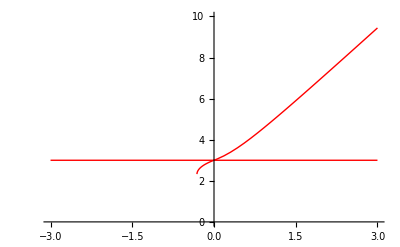

```mathematica
Plot[{σ[3,2,1,ξ][[2]],3},{ξ,-3,3}, PlotStyle->{{Red, Thick}, {Red}}, PlotRange->{0,10}]
```

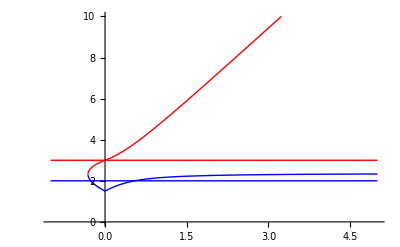

```mathematica
Plot[{σ[3,2,1,ξ][[2]],3,σ[3,2,1,ξ][[1]], 2},{ξ,-1,5}, PlotStyle->{{Red, Thick}, {Red},{Blue, Thick},{Blue}}, PlotRange->{0,10}]
```

```mathematica
σ[3,2,1,-0.5]
```

{2.35355-0.576287 ⅈ,2.35355+0.576287 ⅈ}

```mathematica
N[Limit[σ[3,2,1,ξ],ξ->-∞]]
```

{6.62132,∞}